# GRADOS EN INGENIERÍA TELEMÁTICA E INGENIERÍA DE TECNOLOGÍAS DE TELECOMUNICACIÓN Métodos Matemáticos de las Telecomunicaciones (curso 23 - 24) Practica 3 (1 de 3). Sucesiones y series numéricas.

## Límite de una sucesión de números.

## Ejercicio 1

Observad la diferencia entre un límite funcional (cuando x→∞) y un límite por sucesiones con el siguiente ejemplo:

a) Realizar un dibujo de la función f(x)=(3 x^2+x)/(1+x^2) en el intervalo [1,20] y calcular el lim_(x→∞) f(x)
b) Calcular los 50 primeros términos de la sucesión de término general x_n= (3 n^2+n)/(1+n^2) y calcular el lim_(n→∞) x_n
c) Mostrar en un mismo dibujo la gráfica de f(x) y los 20 términos de la sucesión sobre unos mismos ejes.

A)

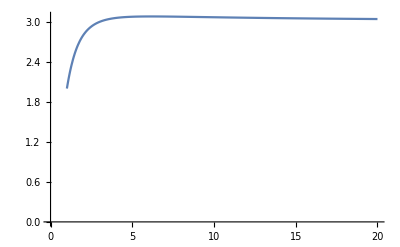

```mathematica
f[x_] := (3x^2 + x) / (1 + x^2)
Plot[f[x], {x, 1, 20}, AxesOrigin->{0,0}]
```

```mathematica
Limit[f[x], x ->∞]
```

3

B)

```mathematica
Table[N[(3 n^2+n)/(1+n^2)], {n,1,50}]
```

{2.,2.8,3.,3.05882,3.07692,3.08108,3.08,3.07692,3.07317,3.06931,3.06557,3.06207,3.05882,3.05584,3.0531,3.05058,3.04828,3.04615,3.0442,3.04239,3.04072,3.03918,3.03774,3.0364,3.03514,3.03397,3.03288,3.03185,3.03088,3.02997,3.02911,3.02829,3.02752,3.02679,3.0261,3.02544,3.02482,3.02422,3.02365,3.02311,3.02259,3.0221,3.02162,3.02117,3.02073,3.02031,3.01991,3.01952,3.01915,3.01879}

```mathematica
Limit[f[x], x ->∞]
```

C)

{2.,2.8,3.,3.05882,3.07692,3.08108,3.08,3.07692,3.07317,3.06931,3.06557,3.06207,3.05882,3.05584,3.0531,3.05058,3.04828,3.04615,3.0442,3.04239}

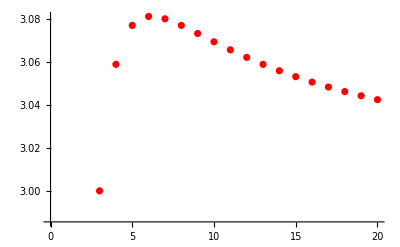

```mathematica
d1 = Plot[f[x], {x, 1, 20}, AxesOrigin->{0,0}];
puntos = Table[N[(3 n^2+n)/(1+n^2)], {n,1,20}]
d2 = ListPlot[puntos, PlotStyle->Red]
```

## Ejercicio 2

Observad la diferencia entre un límite funcional (cuando x→∞) y un límite por sucesiones con el siguiente ejemplo:

a) Realizar un dibujo de la función f(x)=sen(π x ) en el intervalo [1,10] y calcular el lim_(x→∞) f(x)
b) Calcular los 10 primeros términos de la sucesión de término general x_n= sen(π x) y calcular el lim_(n→∞) x_n
c) Mostrar en un mismo dibujo la gráfica de f(x) y los términos de la sucesión.

```mathematica
Clear["Global`*"]
```

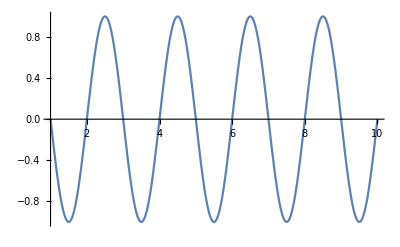

```mathematica
Plot[Sin[Pi * x], {x,1,10}]
```

```mathematica
Limit[Sin[Pi * x], x -> Infinity]
```

Indeterminate

B)

```mathematica
Table[Sin[Pi*n], {n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
DiscreteLimit[Sin[Pi *n], n -> Infinity]
```

0

C)

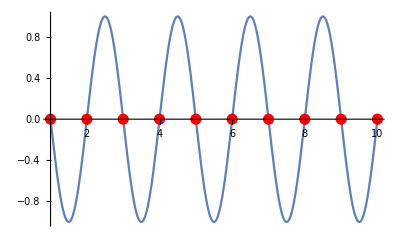

```mathematica
d1 = Plot[Sin[Pi * x], {x, 1, 10}];
puntos = Table[{n, Sin[Pi * n]}, {n,1,10}];
d2 = ListPlot[puntos, PlotStyle->{Red, PointSize[0.02]}];
Show[d1,d2]
```

## Serie numérica.

Dada una sucesión de números reales x_1,x_2,...,x_n,... se llama serie de números reales de término general x_n, y se escribe como ∑_(n=1)^∞ x_n, a la operación de sumar los infinitos términos de la sucesión. La suma de infinitos números reales se define como la combinación de dos operaciones: una suma finita y la operación de paso al límite en la forma que exponemos a continuación.

Sea la sucesión de término general x_n, realizamos las siguientes sumas parciales:

s_1=x_1
s_2=x_1+x_2
⋮      ⋮           ⋮
s_n=x_0+x_1+...+x_n
⋮      ⋮           ⋮

La suma de la serie ∑_(n=1)^∞ x_n, en caso de que exista, será el límite de la suma parcial enésima:

∑_(n=1)^∞ x_n=x_1+x_2+...+x_n+...=lim_(n→∞) s_n

Es decir, la serie ∑_(n=1)^∞ x_n se dice convergente si existe lim_(n→∞) s_n=s. En cuyo caso, a dicho límite se llama suma de la serie y se escribe:

∑_(n=1)^∞ x_n=s

o también:

x_0+x_1+...+x_n,...=s

## Serie geométrica

La serie geométrica de razón r tiene de expresión:

x_1+x_1 r+x_1 r^2+x_1 r^3+...+x_1 r^n+...

que será convergente siempre que el valor absoluto de la razón sea menor que 1:

x_1+x_1 r+x_1 r^2+x_1 r^3+...+x_1 r^n+...=primero/(1-razón)=x_1/(1-r)

## Ejercicio 3

Sea la serie geométrica 1/5+1/10+1/20+1/40+...=1/5·∑_(n=0)^∞ 1/2^n

Se pide:
a) Calcular la suma parcial s_20=1/5+1/10+1/20+...+1/5·1/2^10
b) Calcular la suma parcial de los n primeros sumandos 
c) Calcular la suma de la serie geométrica por la definición (tomando el lim_(n→∞) s_n) y por la fórmula de la suma de una serie geométrica

A)

```mathematica
∑_(k=0)^10 (1/5 * 1/2^k)
```

2047/5120

```mathematica
N[%]
```

0.399805

B)

```mathematica
S[n_] =∑_(k=0)^n (1/5 * 1/2^k)
```

1/5 2^-n (-1+2^(1+n))

C)

```mathematica
DiscreteLimit[S[n], n-> Infinity]
```

2/5

```mathematica
x[n_] = 1/5 * 1/2^n
```

2^-n/5

```mathematica
x[0]
```

1/5

```mathematica
x[0] / (1- (1/2))
```

2/5

## Series armónicas

Una serie armónica tiene la forma:

∑_(n=1)^∞ 1/n^α=1+1/2^α+1/3^α+...+1/n^α+...

## Ejercicio 4

Comprobar la convergencia de las series armónicas ∑_(n=1)^∞ 1/n^α=1+1/2^α+1/3^α+...+1/n^α+...

Este tipo de series numéricas convergen si α>1 y divergen si α≤1

1. Cuando α = 1, la serie ∑_(n=1)^∞ 1/n^α=1+1/2^α+1/3^α+...+1/n^α+... que se llama serie armónica principal. Veamos que, efectivamente, esa serie diverge:

```mathematica
∑_(n=1)^∞ 1/n
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

2. Cuando α < 1, la serie ∑_(n=1)^∞ 1/n^α=1+1/2^α+1/3^α+...+1/n^α+... debe ser también divergente (no convergente). Veamos que esto es cierto. Supongamos  α = 1/2, entonces, la serie queda de la forma:

```mathematica
∑_(n=1)^∞ 1/(√n)
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/(√n)

3. Cuando α > 1, la serie ∑_(n=1)^∞ 1/n^α=1+1/2^α+1/3^α+...+1/n^α+... debe ser convergente, veamos que esto es cierto. Supongamos α = 2, entonces ka serie queda de la forma:

```mathematica
∑_(n=1)^∞ 1/n^2
```

π^2/6

Luego, efectivamente, es convergente.
Probemos con α = 3

```mathematica
∑_(n=1)^∞ 1/n^3
```

```mathematica
N[Zeta[3]]
```

1.20206

## Series alternadas

Una serie alternada es aquella que cambia de signo de forma alternativa:

x_1-x_2+x_3-x_4+x_5...±x_n∓...
con x_i≥0

Si |x_i|converge monótonamente a 0, entonces la serie es convergente.

## Ejercicio 5

Calcular la suma de la serie alternada:

1-1/(√2)+1/(√3)-1/(√4)+1/(√5)-...±1/(√n)+...

Podemos expresar esta serie mediante el término general 1/(√n)(-1)^(n - 1). Comprobemos esto mismo:

```mathematica
Table[1/(√n)(-1)^(n-1), {n,1,10}]
```

{1,-1/(√2),1/(√3),-1/2,1/(√5),-1/(√6),1/(√7),-1/(2 √2),1/3,-1/(√10)}

Veamos si esa serie es convergente:

```mathematica
∑_(n=1)^∞ 1/(√n)(-1)^(n-1)
```

-((-1+√2) Zeta[1/2])

```mathematica
N[%]
```

0.604899

Luego, efectivamente, la serie es convergente